```mathematica
Table[Factor[ChromaticPolynomial[allGraphs5[k,"graph"],x]],{k,allGraphs5GeneratorAtomKeys}]//Tally//TableForm
```

(-4+x) (-3+x) (-2+x) (-1+x) x | 1
(-3+x)^2 (-2+x) (-1+x) x | 10
(-2+x) (-1+x) x (7-5 x+x^2) | 15
(-2+x)^3 (-1+x) x | 10
(-1+x) x (-7+10 x-5 x^2+x^3) | 10
(-1+x)^4 x | 5
x^5 | 1

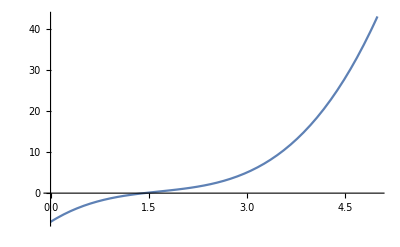

```mathematica
Plot[-7+10 x-5 x^2+x^3,{x,0,5}]
```

```mathematica
Table[TableForm[Table[func[ChromaticPolynomial[allGraphs5[k,"graph"],x]],{k,allGraphs5GeneratorAtomKeys}]//Tally//Sort,TableDepth->1],{func,{CompleteBaseCoeff,NullBaseCoeff,TreeBaseCoeff,CycleBaseCoeff,JacobsthalBaseCoeff}}]
```

{{{0,0,0,0,0,1},1}
{{0,0,0,0,1,1},10}
{{0,0,0,1,2,1},15}
{{0,0,0,1,3,1},10}
{{0,0,1,4,4,1},10}
{{0,0,1,7,6,1},5}
{{0,1,15,25,10,1},1},{{0,0,0,0,0,1},1}
{{0,1,-4,6,-4,1},5}
{{0,7,-17,15,-6,1},10}
{{0,8,-20,18,-7,1},10}
{{0,14,-31,24,-8,1},15}
{{0,18,-39,29,-9,1},10}
{{0,24,-50,35,-10,1},1},{{0,0,-6,11,-6,1},1}
{{0,0,-4,8,-5,1},10}
{{0,0,-3,6,-4,1},15}
{{0,0,-1,3,-3,1},10}
{{0,0,-1,3,-2,1},10}
{{0,0,0,0,0,1},5}
{{0,1,4,6,4,1},1},{{0,0,0,0,1,1},5}
{{0,0,2,0,-2,1},10}
{{0,0,2,1,-1,1},10}
{{0,0,3,2,-3,1},15}
{{0,0,4,3,-4,1},10}
{{0,0,5,5,-5,1},1}
{{0,1,10,10,5,1},1},{{0,0,0,0,-1,1},1}
{{0,0,0,0,0,1},10}
{{0,0,0,1,1,1},15}
{{0,0,0,1,2,1},10}
{{0,0,1,4,3,1},10}
{{0,0,1,7,5,1},5}
{{0,1,15,25,9,1},1}}

```mathematica
TableForm[Table[{ChromaticPolynomial[allGraphs5[k,"graph"],x],Discriminant[ChromaticPolynomial[allGraphs5[k,"graph"],x],x]},{k,allGraphs5GeneratorAtomKeys}]//Tally//Sort,TableDepth->1]
```

{{x^5,0},1}
{{24 x-50 x^2+35 x^3-10 x^4+x^5,82944},1}
{{18 x-39 x^2+29 x^3-9 x^4+x^5,0},10}
{{14 x-31 x^2+24 x^3-8 x^4+x^5,-5292},15}
{{8 x-20 x^2+18 x^3-7 x^4+x^5,0},10}
{{7 x-17 x^2+15 x^3-6 x^4+x^5,-1127},10}
{{x-4 x^2+6 x^3-4 x^4+x^5,0},5}

```mathematica
TableForm[Table[{ChromaticPolynomial[allGraphs5[k,"graph"],x],Discriminant[ChromaticPolynomial[allGraphs5[k,"graph"],x],x]},{k,allGraphs5FakeAtomKeys}]//Tally//Sort,TableDepth->1]
```

{{x^5,0},1}
{{24 x-50 x^2+35 x^3-10 x^4+x^5,82944},1}
{{-6 x^2+11 x^3-6 x^4+x^5,0},5}
{{-2 x^2+5 x^3-4 x^4+x^5,0},10}
{{2 x^3-3 x^4+x^5,0},10}
{{x^3-2 x^4+x^5,0},15}
{{-x^4+x^5,0},10}

```mathematica
sorted=Bases["G","AtomKeys"];
```

```mathematica
BaseCoeff[sorted[[1]],"C"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Bases["G","AtomKeys"]
```

{29524,29523,29515,29521,29281,29443,29497,9841,22963,27337,28795,29280,29440,29488,9840,9832,9838,22962,22882,22936,27334,27094,27310,28786,28552,28714,29511,29191,29251,29415,3037,7573,9085,20767,22231,26607,9828,3036,7570,9076,22854,20740,22150,27064,26364,28462,29160,760,2278,6816,20034,0}

```mathematica
ChromaticPolynomial[allGraphs5[sorted[[1]],"graph"],x]//Factor
```

(-4+x) (-3+x) (-2+x) (-1+x) x

```mathematica
allGraphs5[sorted[[20]],"colofourrealnull"]
```

14 n12345-4 n1234x5-3 n1235x4-n123x45+n123x4x5-4 n1245x3-2 n124x35+2 n124x3x5-n125x34+n125x3x4-2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5-4 n1345x2+n134x2x5-n135x24+n135x2x4-2 n145x23+2 n145x2x3-n14x235+n14x23x5+n14x2x35-n14x2x3x5-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4-4 n1x2345+2 n1x234x5+n1x235x4+n1x23x45-n1x23x4x5+n1x245x3+n1x24x35-n1x24x3x5+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5

```mathematica
Table[
With[
{base="C"},
allGraphs5[k,Bases[base,"Colofour"]]/.RepChrom[base]
],
{k,sorted}
]//Tally//Sort//TableForm
```

x^5-10 x^4+35 x^3-50 x^2+24 x | 1
(x^4-6 x^3+11 x^2-6 x)+(x^5-10 x^4+35 x^3-50 x^2+24 x) | 10
(x^3-3 x^2+2 x)+2 (x^4-6 x^3+11 x^2-6 x)+(x^5-10 x^4+35 x^3-50 x^2+24 x) | 15
(x^3-3 x^2+2 x)+3 (x^4-6 x^3+11 x^2-6 x)+(x^5-10 x^4+35 x^3-50 x^2+24 x) | 10
(x^2-x)+4 (x^3-3 x^2+2 x)+4 (x^4-6 x^3+11 x^2-6 x)+(x^5-10 x^4+35 x^3-50 x^2+24 x) | 10
(x^2-x)+7 (x^3-3 x^2+2 x)+6 (x^4-6 x^3+11 x^2-6 x)+(x^5-10 x^4+35 x^3-50 x^2+24 x) | 5
x+15 (x^2-x)+25 (x^3-3 x^2+2 x)+10 (x^4-6 x^3+11 x^2-6 x)+(x^5-10 x^4+35 x^3-50 x^2+24 x) | 1

```mathematica
ChromaticPolynomial[allGraphs5[sorted[[20]],"graph"],x]//Factor
```

(-2+x) (-1+x) x (7-5 x+x^2)

```mathematica
Clear[RepChrom];RepChrom[base_]:=RepChrom[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->Style[TraditionalForm[ChromaticPolynomial[allGraphs5[key,"graph"],x]],Darker[Green]],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
RepChrom["C"]
```

{v1x2x3x4x5→(x-4) (x-3) (x-2) (x-1) x,v1x2x3x45→(x-3) (x-2) (x-1) x,v1x2x34x5→(x-3) (x-2) (x-1) x,v1x2x35x4→(x-3) (x-2) (x-1) x,v1x23x4x5→(x-3) (x-2) (x-1) x,v1x24x3x5→(x-3) (x-2) (x-1) x,v1x25x3x4→(x-3) (x-2) (x-1) x,v12x3x4x5→(x-3) (x-2) (x-1) x,v13x2x4x5→(x-3) (x-2) (x-1) x,v14x2x3x5→(x-3) (x-2) (x-1) x,v15x2x3x4→(x-3) (x-2) (x-1) x,v1x23x45→(x-2) (x-1) x,v1x24x35→(x-2) (x-1) x,v1x25x34→(x-2) (x-1) x,v12x3x45→(x-2) (x-1) x,v12x34x5→(x-2) (x-1) x,v12x35x4→(x-2) (x-1) x,v13x2x45→(x-2) (x-1) x,v13x24x5→(x-2) (x-1) x,v13x25x4→(x-2) (x-1) x,v14x2x35→(x-2) (x-1) x,v14x23x5→(x-2) (x-1) x,v14x25x3→(x-2) (x-1) x,v15x2x34→(x-2) (x-1) x,v15x23x4→(x-2) (x-1) x,v15x24x3→(x-2) (x-1) x,v1x2x345→(x-2) (x-1) x,v1x234x5→(x-2) (x-1) x,v1x235x4→(x-2) (x-1) x,v1x245x3→(x-2) (x-1) x,v123x4x5→(x-2) (x-1) x,v124x3x5→(x-2) (x-1) x,v125x3x4→(x-2) (x-1) x,v134x2x5→(x-2) (x-1) x,v135x2x4→(x-2) (x-1) x,v145x2x3→(x-2) (x-1) x,v12x345→(x-1) x,v123x45→(x-1) x,v124x35→(x-1) x,v125x34→(x-1) x,v13x245→(x-1) x,v134x25→(x-1) x,v135x24→(x-1) x,v14x235→(x-1) x,v145x23→(x-1) x,v15x234→(x-1) x,v1x2345→(x-1) x,v1234x5→(x-1) x,v1235x4→(x-1) x,v1245x3→(x-1) x,v1345x2→(x-1) x,v12345→x}

```mathematica
Tab
```

```mathematica
With[{m=ConversionMatrix["G","C"]},Table[Total[Table[m[[i,j]],{j,52}]],{i,1,52}]]
```

{1,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,10,10,10,10,10,10,10,10,10,10,15,15,15,15,15,52}

```mathematica
With[{m=ConversionMatrix["G","C"]},MatrixForm[m,TableHeadings->{Table[Total[Table[m[[i,j]],{j,1,52}]],{i,1,52}], Table[Total[Table[m[[j,i]],{j,52}]],{i,1,52}]}]]
```

( | 52 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
15 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
15 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
15 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
15 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
15 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
52 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
]
```

```mathematica
Table[With[{g=allGraphs5[k,"graph"]},Labeled[g,Factor[ChromaticPolynomial[g,x]]]],{k,allGraphs5GeneratorAtomKeys}]
```

{-Graphics-(-4+x) (-3+x) (-2+x) (-1+x) x,-Graphics-(-3+x)^2 (-2+x) (-1+x) x,-Graphics-(-3+x)^2 (-2+x) (-1+x) x,-Graphics-(-3+x)^2 (-2+x) (-1+x) x,-Graphics-(-3+x)^2 (-2+x) (-1+x) x,-Graphics-(-3+x)^2 (-2+x) (-1+x) x,-Graphics-(-3+x)^2 (-2+x) (-1+x) x,-Graphics-(-3+x)^2 (-2+x) (-1+x) x,-Graphics-(-3+x)^2 (-2+x) (-1+x) x,-Graphics-(-3+x)^2 (-2+x) (-1+x) x,-Graphics-(-3+x)^2 (-2+x) (-1+x) x,-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x) (-1+x) x (7-5 x+x^2),-Graphics-(-2+x)^3 (-1+x) x,-Graphics-(-2+x)^3 (-1+x) x,-Graphics-(-2+x)^3 (-1+x) x,-Graphics-(-2+x)^3 (-1+x) x,-Graphics-(-2+x)^3 (-1+x) x,-Graphics-(-2+x)^3 (-1+x) x,-Graphics-(-2+x)^3 (-1+x) x,-Graphics-(-2+x)^3 (-1+x) x,-Graphics-(-2+x)^3 (-1+x) x,-Graphics-(-2+x)^3 (-1+x) x,-Graphics-(-1+x) x (-7+10 x-5 x^2+x^3),-Graphics-(-1+x) x (-7+10 x-5 x^2+x^3),-Graphics-(-1+x) x (-7+10 x-5 x^2+x^3),-Graphics-(-1+x) x (-7+10 x-5 x^2+x^3),-Graphics-(-1+x) x (-7+10 x-5 x^2+x^3),-Graphics-(-1+x) x (-7+10 x-5 x^2+x^3),-Graphics-(-1+x) x (-7+10 x-5 x^2+x^3),-Graphics-(-1+x) x (-7+10 x-5 x^2+x^3),-Graphics-(-1+x) x (-7+10 x-5 x^2+x^3),-Graphics-(-1+x) x (-7+10 x-5 x^2+x^3),-Graphics-(-1+x)^4 x,-Graphics-(-1+x)^4 x,-Graphics-(-1+x)^4 x,-Graphics-(-1+x)^4 x,-Graphics-(-1+x)^4 x,-Graphics-x^5}

```mathematica
Factor[ChromaticPolynomial[allGraphs5[K5Key,"graph"],x]-ChromaticPolynomial[allGraphs5[K4Key,"graph"],x]]
```

-4 (-3+x) (-2+x) (-1+x) x

```mathematica
Discriminant[18 x-39 x^2+29 x^3-9 x^4+x^5,x]
```

0

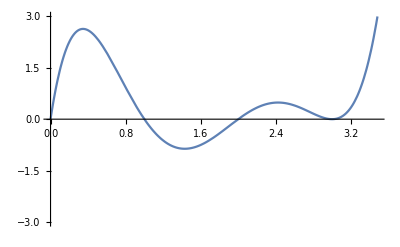

```mathematica
Plot[18 x-39 x^2+29 x^3-9 x^4+x^5,{x,0,5},PlotRange->{All,{-3,3}}]
```